# Linearized BBM Notebook

Solves the eigenvalue problem associated to the linearization of the Benjamin-Bona-Mahony equation around a periodic (elliptic function) traveling wave. The notebook computes the spectrum on  using a spectral decomposition and also computes the Hamiltonian Floquet discriminant and bifurcation index using the Mathematica ODE solver. The solutions are computed using the exact elliptic function formulas but are checked at certain points by numerical solution of the traveling wave ODEs. 

The code below solves the traveling wave ODE.

```mathematica
pexp = 2;
c=1;
En = -1;
a = 7/6;
Abel[ϕ_,E_,a_,c_] := 2 E/c + 2 a ϕ/c + (1-c) ϕ^2/c -2 ϕ^(pexp+1)/( c pexp(pexp+1))
RootList=N[x /.Solve[Abel[x,En,a,c]==0,x,Reals,WorkingPrecision->30]];
root2=RootList[[Dimensions[RootList][[1]]]];
root1=RootList[[Dimensions[RootList][[1]]-1]];
avg = (root2+root1)/2;
rad = (root2-root1)/2;
ReducedPoly = PolynomialQuotient[Abel[x,En,a,c],(x-root1)(root2-x),x];
Period = NIntegrate[1/Sqrt[ReducedPoly /. x -> avg + rad Sin[Θ]],{Θ,-Pi,Pi}];
WaveProfile = NDSolveValue[{c y''[x]==a -(1- c) y[x] - y[x]^(pexp)/pexp  ,y[0]==root2,y'[0]==0},y,{x,0,2 Period},AccuracyGoal->13,PrecisionGoal->13];
mm = 0.2;
KI = EllipticK[mm];
KIP = EllipticK[1-mm];
EI = EllipticE[mm];
qq = Exp[- Pi KIP/KI];
A0 = 1 + (EI - (1-mm) KI)/(mm KI);
An[k_] := 2 Pi^2/(mm KI^2) k qq^k/(1-qq^(2k))
nmodes = 15;
PFC = Join[{A0},Table[An[k]/2,{k,1,2*nmodes}]];
WaveProfileF[x_]:= A0 + Sum[An[k]Cos[Pi k x/KI Sqrt[5/12]],{k,1,nmodes}]
WP[x_] := 1+(JacobiCN[Sqrt[5/12]x,1/5])^2
WPP[x_] := -√(5/3) JacobiCN[1/2 √(5/3) x,1/5] JacobiDN[1/2 √(5/3) x,1/5] JacobiSN[1/2 √(5/3) x,1/5]
```

The plots below depict the numerical solution of the wave profile and the derivative of the wave profile, and the difference between the wave profile output from the ODE solver and the elliptic function wave profile, as well as the difference between the exact elliptic function wave profile and the the first 2*nmodes+1 terms of the Fourier series for the wave profile. Note that 31 terms of the Fourier series gives a significantly better approximation than the ODE solver.

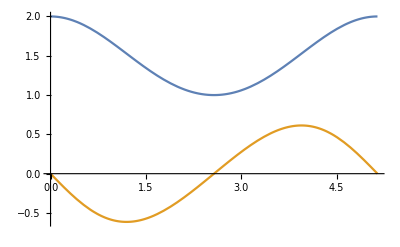

```mathematica
NumPlot=Plot[{WaveProfile[x],WaveProfile'[x]},{x,0,Period}]
```

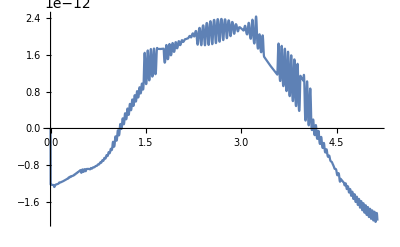

```mathematica
Plot[WaveProfile[x]-(1+(JacobiCN[Sqrt[5/12]x,1/5])^2),{x,0,Period}]
```

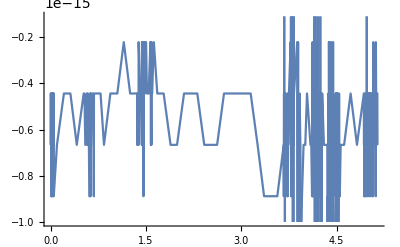

```mathematica
Plot[WaveProfileF[x]-(1+(JacobiCN[Sqrt[5/12]x,1/5])^2),{x,0,Period}]
```

Set up the matrices needed for the spectral method. We are solving , where  is the Floquet exponent or quasi-momentum. We will repeatedly solve this eigenvalue problem for different value of μ. As set up μ ranges over the interval .

```mathematica
κ=2 Pi/Period;
J[μ_]:= DiagonalMatrix[Table[I (k+μ)κ/(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
D1[μ_]:= DiagonalMatrix[Table[I (k+μ)κ,{k,-nmodes,nmodes}]]
P[μ_] :=  DiagonalMatrix[Table[(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
L[μ_] := DiagonalMatrix[Table[κ^2(k+μ)^2,{k,-nmodes,nmodes}]]
qm = ToeplitzMatrix[PFC];
```

At μ=0 the problem should have a zero eigenvalue of algebraic multiplicity three, geometric multiplicity two. This is a good test of the accuracy of the numerics. Here we see that the error in the zero eigenvalues is of order .

```mathematica
Chop[Eigenvalues[J[0].(L[0]-qm)]]
```

{0.+18.1934 ⅈ,0.-18.1934 ⅈ,0.-16.9618 ⅈ,0.+16.9618 ⅈ,0.+15.7288 ⅈ,0.-15.7288 ⅈ,0.-14.494 ⅈ,0.+14.494 ⅈ,0.+13.257 ⅈ,0.-13.257 ⅈ,0.+12.0169 ⅈ,0.-12.0169 ⅈ,0.+10.773 ⅈ,0.-10.773 ⅈ,0.+9.52361 ⅈ,0.-9.52361 ⅈ,0.+8.26672 ⅈ,0.-8.26672 ⅈ,0.+6.99875 ⅈ,0.-6.99875 ⅈ,0.-5.71364 ⅈ,0.+5.71364 ⅈ,0.+4.40017 ⅈ,0.-4.40017 ⅈ,0.-3.03599 ⅈ,0.+3.03599 ⅈ,0.+1.57543 ⅈ,0.-1.57543 ⅈ,3.18973×10^-8,-3.18973×10^-8,0}

The code below computes the eigenvalues as μ varies over .

```mathematica
evals=Flatten[Table[Chop[Eigenvalues[J[x].(L[x]-qm)]],{x,-1/2,1/2,.001}]];
```

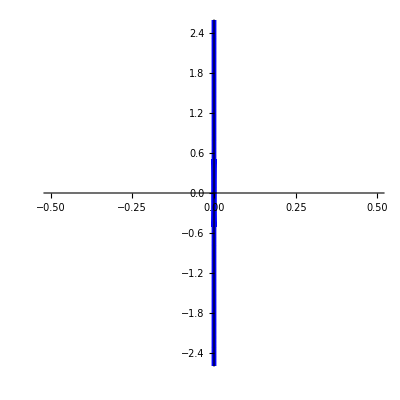

```mathematica
SFig=ComplexListPlot[evals,PlotStyle->{Blue,PointSize[Small]},PlotRange->{{-0.5,0.5},{-2.5,2.5}},AspectRatio->1]
```

```mathematica
Max[Abs[Re[evals]]]
```

3.18973×10^-8

The code below solves the ODE associated with the linearized operator in order to construct the monodromy map and bifurcation index. The quantities dp[x], dq[x], dr[x] are the derivatives with respect to λ of p[x],q[x],r[x].

```mathematica
sols1=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-WPP[x] p[x] - WP[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - WPP[x] dp[x] - WP[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==1,q[0]==0,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols2=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-WPP[x] p[x] - WP[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - WPP[x] dp[x] - WP[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==1,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols3=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-WPP[x] p[x] - WP[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - WPP[x] dp[x] - WP[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==0,r[0]==1,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
```

```mathematica
mon[λ_?NumericQ] := {{sols1[λ][[1]][Period],sols2[λ][[1]][Period],sols3[λ][[1]][Period]},{sols1[λ][[2]][Period],sols2[λ][[2]][Period],sols3[λ][[2]][Period]},{sols1[λ][[3]][Period],sols2[λ][[3]][Period],sols3[λ][[3]][Period]}};
CharPoly[λ_?NumericQ] :=CharacteristicPolynomial[mon[λ],μ];
f[λ_?NumericQ]:=sols1[λ][[1]][Period]+sols2[λ][[2]][Period]+sols3[λ][[3]][Period]
fp[λ_?NumericQ] :=sols1[λ][[4]][Period]+sols2[λ][[5]][Period]+sols3[λ][[6]][Period]
g[λ_?NumericQ] := -1/2(Tr[mon[λ]]^2-Tr[mon[λ].mon[λ]]);
h[λ_?NumericQ] := -Conjugate[g[λ]Exp[-Period λ]];
Δ[λ_?NumericQ] := Det[mon[λ]] Exp[-Period λ];
Φ[λ_?NumericQ] := Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]
Multi[λ_?NumericQ] := If[Re[Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]]<0,1,I]
CP[F_,λ_] := -x^3 + F[λ] x^2 - F[-λ] Exp[Period λ/c] x + Exp[Period λ/c]
```

Again a check of accuracy: the monodromy matrix at λ=0 should have μ=1 as an eigenvalue of multiplicity three. We can see that this is the case.

```mathematica
mon[0.0]
```

{{1.,-7.98882×10^-9,5.78768×10^-9},{-1.99746,1.,-1.11141},{6.46883×10^-8,2.11636×10^-8,1.}}

```mathematica
CharPoly[0.0]
```

1.-3. μ+3. μ^2-μ^3

Mark the regions of higher spectral multiplicity with parallel magenta lines.

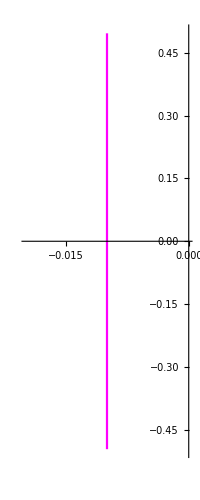

```mathematica
S1a = ParametricPlot[{.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta];
S1b = ParametricPlot[{-.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta]
```

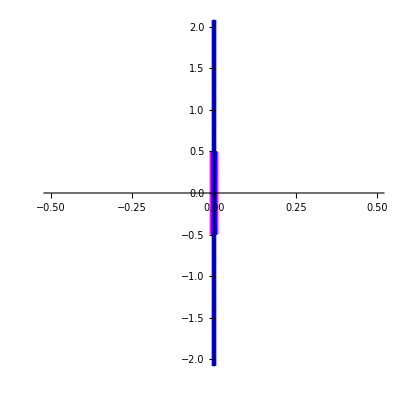

```mathematica
PaperFig=Show[SFig,S1a,S1b,PlotRange->{{-0.5,0.5},{-2,2}}]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/BBMStableFigure.png",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/BBMStableFigure.png

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/BBMStableFigure.pdf",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/BBMStableFigure.pdf

```mathematica
Show[%120,PlotRange->{{-.5,.5},{-2,2}}]
```

Show::gtype: Out is not a type of graphics.

Show[%120,PlotRange→{{-0.5,0.5},{-2,2}}]

```mathematica
Res1 = Expand[Resultant[CP[F,λ],D[CP[F,λ],λ],x]Exp[-3Period λ/c]]
```

135.968-135.968 F[-λ] F[λ]+26.4418 ⅇ^(5.14216 λ) F[-λ]^2 F'[-λ]+26.4418 F[λ] F'[-λ]-10.2843 ⅇ^(5.14216 λ) F[-λ] F'[-λ]^2+1. ⅇ^(5.14216 λ) F'[-λ]^3+26.4418 F[-λ] F'[λ]+26.4418 ⅇ^(-5.14216 λ) F[λ]^2 F'[λ]-15.4265 F'[-λ] F'[λ]-5.14216 F[-λ] F[λ] F'[-λ] F'[λ]+1. F[λ] F'[-λ]^2 F'[λ]-10.2843 ⅇ^(-5.14216 λ) F[λ] F'[λ]^2+1. F[-λ] F'[-λ] F'[λ]^2+1. ⅇ^(-5.14216 λ) F'[λ]^3

```mathematica
Res1 /. {F[λ] -> H, F[-λ]-> HC,F'[λ]->HP,F'[-λ]->HPC}
```

135.968-135.968 H HC+26.4418 ⅇ^(-5.14216 λ) H^2 HP+26.4418 HC HP-10.2843 ⅇ^(-5.14216 λ) H HP^2+1. ⅇ^(-5.14216 λ) HP^3+26.4418 H HPC+26.4418 ⅇ^(5.14216 λ) HC^2 HPC-15.4265 HP HPC-5.14216 H HC HP HPC+1. HC HP^2 HPC-10.2843 ⅇ^(5.14216 λ) HC HPC^2+1. H HP HPC^2+1. ⅇ^(5.14216 λ) HPC^3

```mathematica
Bifurcation[H_,HC_,HP_,HPC_,λ_] := 135.96766963553404-135.96766963553404 H HC+26.44176469501827 ⅇ^(-5.142155646712599 λ) H^2 HP+26.44176469501827 HC HP-10.2843112934252 ⅇ^(-5.142155646712599 λ) H HP^2+1. ⅇ^(-5.142155646712599 λ) HP^3+26.44176469501827 H HPC+26.44176469501827 ⅇ^(5.142155646712599 λ) HC^2 HPC-15.426466940137798 HP HPC-5.1421556467126 H HC HP HPC+1. HC HP^2 HPC-10.2843112934252 ⅇ^(5.142155646712599 λ) HC HPC^2+1. H HP HPC^2+1. ⅇ^(5.142155646712599 λ) HPC^3
```

```mathematica
Bif2[λ_?NumericQ] := Bifurcation[f[λ],Conjugate[f[λ]],fp[λ],Conjugate[fp[λ]],λ]
```

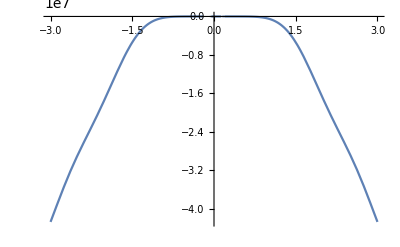

```mathematica
Plot[Bif2[I y],{y,-3,3}]
```

The bifurcation index appears to have no roots apart from the (non-generic) root at λ=0.